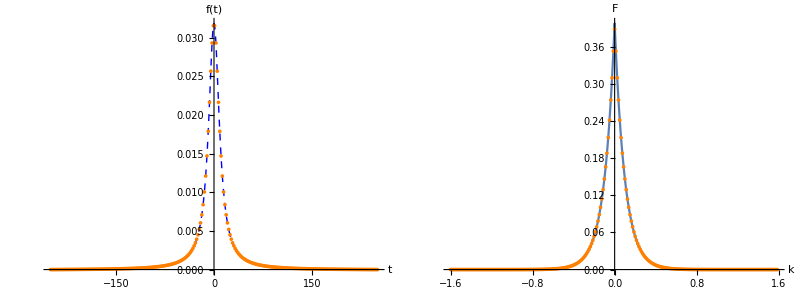

```mathematica
sm=250;
n=2^8;
ds=2 sm/(n-1);
grid=Range[-sm,sm,ds];

(*f[σ_]:=Exp[-3.3 (σ)^2];*)
si=10.0;
f[es_]:=si/Pi 1/((es)^2+si^2);
samples=f/@grid;

factor=ds Sqrt[n/(2 Pi)] Exp[-I Pi (n-1)/n Range[0,n-1]];

transform=Chop[Fourier[samples] factor];
Fc[k_]:=FourierTransform[f[σ],σ,k];

km=(n-1)/2 Pi/sm;
dk=(n-2)/(n-1) Pi/(2 sm);
freq=RotateRight[Range[-n/2,n/2-1],n/2] 2 dk;

Grid[{{
Show[
Plot[f[x],{x,grid[[1]],grid[[-1]]},AxesLabel->{"t","f(t)"},PlotRange->Full,PlotStyle->{Blue,Dashed,Thick},ImageSize->Medium]
,
ListPlot[Table[{grid[[j]],samples[[j]]},{j,1,Length[grid]}],PlotStyle->{Orange},PlotRange->Full,ImageSize->Medium]
],
Show[
Plot[Fc[x],{x,Min[freq],Max[freq]},AxesLabel->{"k","F"},PlotRange->Full,ImageSize->Medium],
ListPlot[Transpose[{freq,Abs[transform]}],PlotStyle->{Orange},PlotRange->Full,ImageSize->Medium]
]
}}]
```

```mathematica
si = 10;
a=0.05;
Lorentz[z_]:=si/Pi 1/(z^2+si^2);
r[y_]:=Sqrt[y] Exp[-a y] HeavisideTheta[y]
Lit[s_]:=NIntegrate[r[y] Lorentz[y-s],{y,0,100}]
```

```mathematica
sm=2000;
n=2^10;
ds=2 sm/(n-1);
grid=Range[-sm,sm,ds];

LitData=Lit/@grid;
LorentzData=Lorentz/@grid;

factor=ds Sqrt[n/(2 Pi)] Exp[-I Pi (n-1)/n Range[0,n-1]];

FLitData=Chop[Fourier[LitData] factor];
FLorentzData=Chop[Fourier[LorentzData] factor];
FLorentz[k_]:=1/Sqrt[2 Pi] Exp[-si Abs[k]];
(*Fc[k_]:=FourierTransform[Lit[σ],σ,k];*)

dk=Pi/(2 sm);
freq=RotateRight[Range[-n/2,n/2-1],n/2] 2 dk;
```

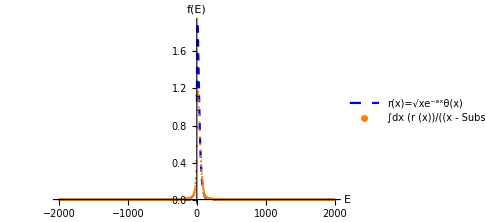
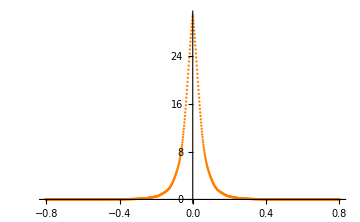
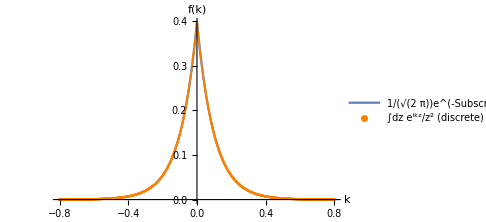
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{
Show[
Plot[r[x],{x,grid[[1]],grid[[-1]]},AxesLabel->{"E","f(E)"},PlotRange->Full,PlotStyle->{Blue,Dashed,Thick},ImageSize->Medium,PlotLegends->{"r(x)=√xe^-axθ(x)"}]
,
ListPlot[Table[{grid[[j]],LitData[[j]]},{j,1,Length[grid]}],PlotStyle->{Orange},PlotRange->Full,ImageSize->Medium,PlotLegends->{"∫dx (r (x))/(x - SubscriptBox[σ, r])^2"}]
],
Show[
(*Plot[Fc[x],{x,Min[freq],Max[freq]},AxesLabel->{"k","F"},PlotRange->Full,ImageSize->Medium],*)
ListPlot[Transpose[{freq,Abs[FLitData]}],PlotStyle->{Orange},PlotRange->Full,ImageSize->Medium]
],
Show[
Plot[FLorentz[x],{x,Min[freq],Max[freq]},AxesLabel->{"k","f(k)"},PlotRange->Full,ImageSize->Medium,PlotLegends->{"1/(√(2  π))e^(-SubscriptBox[σ, i] | k |)"}],
ListPlot[Transpose[{freq,Abs[FLorentzData]}],PlotStyle->{Orange},PlotRange->Full,ImageSize->Medium,PlotLegends->{"∫dz e^ikz/z^2 (discrete)"}]
]
}}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

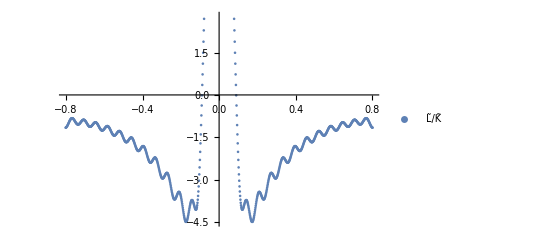
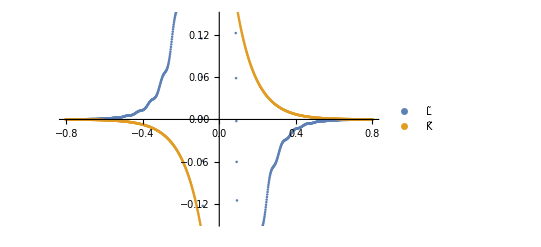
-Graphics- | -Graphics-

```mathematica
Grid[{{ListPlot[Transpose[{freq,Re[FLitData]/Re[FLorentzData]}],PlotLegends->{"L̃/K̃"}],ListPlot[{Transpose[{freq,Re[FLitData]}],Transpose[{freq,Re[FLorentzData]}]},PlotLegends->{"L̃","K̃"}]}}]
```

```mathematica
ECCE poles!
```